# Construct the grid to output the h^ret data on

### Old grid (deprecated)

```mathematica
(*r0=175;
Δr=4;
ra=r0-Δr;
rb=r0+Δr;

grid[1]=Table[r,{r,ra,rb,1/100}];(*Dense around the particle*)
grid[2]=Table[r,{r,rb,100,1/10}];
grid[3]=Table[r,{r,100,1000,1}];
grid[4]=Table[r,{r,1000,10000,10}];
grid[5]=Table[r,{r,2,ra,10^-2}][[2;;]];(*Change this for large r0*)
grid[6]=Table[r,{r,2,3,10^-2}][[2;;]];
grid[7]=Table[r,{r,2,2+10^-2,10^-3}][[2;;]];
grid[8]=Table[r,{r,2,2+10^-3,10^-4}][[2;;]];
grid[9]=Table[r,{r,2,2+10^-4,10^-5}][[2;;]];

res=Sort[Union[Flatten[Table[grid[i],{i,1,9}]]],Less];
importantIndexes=Flatten[{Position[res,ra],Position[res,r0],Position[res,rb]}];*)
```

```mathematica
(*importantIndexes*)
```

```mathematica
(*Length[res]*)
```

```mathematica
(*Nr0[r_Integer]:=r
Nr0[r_]:=N[r]*)
```

```mathematica
(*SetDirectory[NotebookDirectory[]<>"../input/"]
Export["radial_grid_r"<>ToString[Nr0[r0]]<>".h5",{res,importantIndexes},{"Datasets",{"r","ImportantIndexes"}}]*)
```

### New grid

```mathematica
<<SimulationTools`
```

```mathematica
r0=8.9;
Δr0=If[r0≤20,2,4];
```

```mathematica
M=1;
```

```mathematica
V1Boundary = 2+1/2M;
rin = 2+10^-5;
```

```mathematica
rs[r_]:=r+2 Log[-1+r/2]
```

```mathematica
rOfrs[rs1_]:=r/.Quiet@FindRoot[rs[r]==rs1,{r,2+10^-10,100},WorkingPrecision->30]
```

```mathematica
rsValues=Subdivide[rs[rin],rs[V1Boundary],500];
```

```mathematica
rValues=rOfrs/@rsValues;
```

```mathematica
1-rs[rValues]/rsValues//Max
```

3.61267671×10^-17

```mathematica
V1Region = rValues;
V2Region=Table[r,{r,V1Boundary,r0-Δr0,0.01}][[2;;]];
TRegion = Table[r,{r,r0-Δr0,r0+Δr0,0.01}][[2;;]];
U1Region=Table[r,{r,r0+Δr0,100,0.1}][[2;;]];
U2Region=Table[r,{r,100,1000,0.5}][[2;;]];
U3Region=Table[r,{r,1000,10^4,4}][[2;;]];
```

```mathematica
grid=Union@N[Join[V1Region,V2Region,TRegion,U1Region,U2Region,U3Region]];
```

```mathematica
Length[grid]
```

6282

```mathematica
f[r_]:=1-2/r;
```

```mathematica
func[r_]:=f[r] 1/r
```

```mathematica
funcOnGrid={grid,func[grid]}//Transpose//ToDataTable;
```

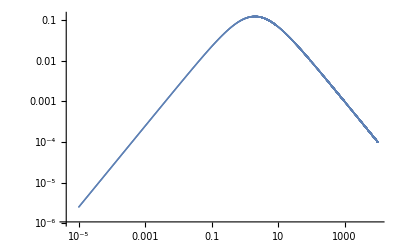

```mathematica
ListLogLogPlot[Shifted[funcOnGrid,-2]]
```

## Grid integration functions

```mathematica
UniformGridIntegrate[dt_,halfOpen_:0]:=Module[{f=ToListOfData[dt],x=ToListOfCoordinates[dt],Δx},
Δx=Abs[x[[1]]-x[[2]]];
If[Length[f]≥6,
Δx/24(If[halfOpen==2,{17,-7,2}.f[[1;;3]],0]+{9,28,23}.f[[1;;3]]+24Total[f[[4;;-4]]]+{23,28,9}.f[[-3;;]] +If[halfOpen==1,{2,-7,17}.f[[-3;;]],0]),
Δx/24({10,26}.f[[1;;2]]+24Total[f[[3;;-3]]]+{26,10}.f[[-2;;]] + If[halfOpen==1,{-3,15}.f[[-2;;]],0])
]
]
```

```mathematica
gridIntegrate[dt_]:=Module[{f,Δx,x},
If[Length[dt]==1 || Length[dt]==0,Return[0]];
If[UniformGridQ[dt],
UniformGridIntegrate[dt],
UniformGridIntegrate[dt[[;;-2]],1]
]
]
```

```mathematica
DownsampleRegion[dt_,n_]:=Module[{f=ToList[dt]},
If[Length[dt]==0,Return[{}]];
ToDataTable[Union[Downsample[dt,n]//ToList,{f[[1]],f[[-1]]}]]
]
```

## Check well the integration works in the near-horizon region

```mathematica
rVals=(Slab[funcOnGrid,2;;2.5]//ToList//Transpose)[[1]];
```

```mathematica
test={rs[(Slab[funcOnGrid,2;;2.5]//ToList//Transpose)[[1]]],f[rVals]((Slab[funcOnGrid,2;;2.5]//ToList//Transpose)[[2]])}//Transpose//ToDataTable
```

DataTable[<501>,{{-22.4121,-0.272589}}]

```mathematica
UniformGridQ[test]
```

True

```mathematica
gridIntegrate[test]
Integrate[func[r],{r,2+10^-5,2+1/2}]//N
1-%/%%//Abs
```

0.0231436

0.0231436

1.767×10^-9

```mathematica
importantIndexes=Flatten[{Position[grid,r0-Δr0],Position[grid,r0],Position[grid,r0+Δr0]}]
```

{941,1141,1341}

```mathematica
Nr0[r_Integer]:=r
Nr0[r_]:=N[r]
```

```mathematica
SetDirectory[NotebookDirectory[]<>"../input/"]
Export["radial_grid_r"<>ToString[Nr0[r0]]<>".h5",{grid,importantIndexes},{"Datasets",{"r","ImportantIndexes"}}]
```

/Users/niels/Code/SecondOrder/h1Lorenz/input

radial_grid_r8.9.h5

```mathematica
Quit[]
```